### Functions for skew-symmetric Parlett-Reid tridiagonalization and the corresponding Pfaffian routine

Compute the LTL decomposition of a skew-symmetric matrix using the Parlett-Reid algorithm. The function return T, L and P, where T is a tridiagonal matrix, L a unit lower triangulat matrix and P a permutation matrix, such that P A P^T = L T L^T .
Note that this function is not needed for the Pfaffian computation, but is only provided fro demontration purposes.

```mathematica
SkewLTL[Mat_]:=Module[{A,L,Pv, N, ip},
A=Mat;
N=Dimensions[A][[1]];
L=IdentityMatrix[N];
Pv=Range[N];
For[i=1, i<N-1, i++,
(*find out the maximum entry in the column i, starting from row i+1*)
ip=i+Position[Abs[A[[i+1;;, i]]], Max[Abs[A[[i+1;;,i]]]]][[1,1]];
(*if the maximum entry is not at i+1, permute the matrix so that it is*)
If[i+1 ≠ ip, 
(*Interchange rows and columns in A*)
A[[{i+1, ip},;;]]=A[[{ip,i+1},;;]]; 
A[[;;,{i+1, ip}]]=A[[;;,{ip,i+1}]];
(*interchange rows in L; this amounts to accumulating the product of 
individual Gauss eliminations and permutations*)
L[[{i+1,ip},1;;i]]=L[[{ip,i+1},1;;i]];
(*Accumulate the total permutation matrix*)
Pv[[{i+1,ip}]]=Pv[[{ip,i+1}]];
];
(*Build the Gauss vector*)
L[[i+2;;,i+1]]=A[[i+2;;,i]]/A[[i+1,i]];
(*Row and column i are eliminated*)
A[[i+2;;,i]]=0;A[[i,i+2;;]]=0;
(*Update the remainder of the matrix using an outer product skew-symmetric update. Note that
column and row i+1 are not affected by the update*)
A[[i+2;; , i+2;; ]]+=Transpose[{L[[i+2;;,i+1]]}].{A[[i+2;;,i+1]]}-Transpose[{A[[i+2;;,i+1]]}].{ L[[i+2;;,i+1]]};
];
Return[{A,L,SparseArray[{i_,i_}->1,{N,N}][[Pv]]}]
]
```

Compute the Pfaffian of a skew-symmetric matrix using the LTL decomposition

```mathematica
PfaffianLTL[Mat_]:=Module[{A, N, ip, pfaff},
A=Mat;
N=Dimensions[A][[1]];
If[OddQ[N], Return[0]];
pfaff=1;
For[i=1, i<N-1, i+=2,
(*find out the maximum entry in the column i, starting from row i+1*)
ip=i+Position[Abs[A[[i+1;;, i]]], Max[Abs[A[[i+1;;,i]]]]][[1,1]];
(*if the maximum entry is not at i+1, permute the matrix so that it is*)
If[i+1 ≠ ip, 
(*Interchange rows and columns in A*)
A[[{i+1, ip},;;]]=A[[{ip,i+1},;;]]; 
A[[;;,{i+1, ip}]]=A[[;;,{ip,i+1}]];
(*interchange contributes det(P)=-1*)
pfaff=-pfaff;
];
(*Multiply with every other entry on the diagonal*)
pfaff = pfaff*A[[i,i+1]];
(*Build the Gauss vector*)
A[[i+2;;,i]]=A[[i+2;;,i]]/A[[i+1,i]];
(*Update the remainder of the matrix using an outer product skew-symmetric update. Note that
column and row i+1 are not affected by the update*)
A[[i+2;; , i+2;; ]]+=(#-Transpose[#])&@Outer[Times,A[[i+2;;,i]],A[[i+2;;,i+1]]]
(* The above is much faster than this construct for me: 
Transpose[{A[[i+2;;,i]]}].{A[[i+2;;,i+1]]}-Transpose[{A[[i+2;;,i+1]]}].{ A[[i+2;;,i]]};*)
];
Return[pfaff*A[[N-1,N]]]
]
```

#### Functions for the Householder tridiagonalization and the corresponding Pfaffian routine

The following contains functions to calculate the Pfaffian for real and complex skew-symmetric matrices. Note that the functions don't check (yet) if the inpiut matrix is really skew-symmetric

Function to compute a so-called Householder vector v for x, i.e. a vector such that (1-2/(v^H v) v v^H) * x is a multiple of the unit vector e_1.

```mathematica
HouseholderVectorReal[x_]:=Module[{temp, tempfac, normx},
normx=Norm[x];
If[normx==0, 
Return[{UnitVector[Dimensions[x][[1]],1], 0, 0}],
If[x[[1]]>0,
tempfac=normx,
tempfac=-normx];
temp=x;
temp[[1]]+=tempfac;
Return[{Normalize[temp], 2, -tempfac} ]]]
```

```mathematica
HouseholderVectorComplex[x_]:=Module[{temp, tempfac, normx},
normx=Norm[x];
If[normx==0, 
Return[{UnitVector[Dimensions[x][[1]],1], 0, 0}],
tempfac=ⅇ^(I Arg[x[[1]]]) Norm[x]; 
temp=x;
temp[[1]]+=tempfac;
Return[{Normalize[temp], 2, -tempfac} ]]]
```

Now the functions that do the full tridagonalization that is at the heart of the Pfaffian calculation. For an input matrix A, they return {T,Q} such that A=Q T Q^T . In the real case, this should be the same as what is returned from the HessenbergDecomposition, for the complex case there is no Mathematica equivalent. Note that these functions are not needed for the Pfaffian calculation, they are here merely for testing.

```mathematica
SkewTridiagonalize[Mat_]:=If[MatrixQ[Mat,NumberQ[#]&&!MatchQ[#,_Complex]&],SkewTridiagonalizeReal[Mat],SkewTridiagonalizeComplex[Mat]]
```

```mathematica
SkewTridiagonalizeReal[Mat_]:=Module[{A,Q, v, beta, alpha},
A=Mat;
Q=IdentityMatrix[Dimensions[A][[1]]];
For[i=1,i<Dimensions[A][[1]]-1, i++, 
(*Compute the Householder vector*)
{v,beta, alpha}=HouseholderVectorReal[A[[i+1;; , i]]];
(*eliminate the entries in row and column i*) 
A[[i+1,i]]=alpha;A[[i,i+1]]=-alpha; A[[i+2;;,i]]=0;A[[i,i+2;;]]=0;
(*update the matrix*)
w=beta* A[[i+1;; , i+1;;]].v; 
A[[i+1;; , i+1;; ]]+=Transpose[{v}].{w}-Transpose[{w}].{ v};
(*accumulate the Householder reflections into the full transformation*)
y=Q[[1;;, i+1;;]].v; 
Q[[1;; ,i+1;;]]-=beta*Transpose[{y}].{v}]; 
Return[{A,Q}]]
```

```mathematica
SkewTridiagonalizeComplex[Mat_]:=Module[{A,Q, v, beta, alpha},
A=Mat;
Q=IdentityMatrix[Dimensions[A][[1]]];
For[i=1,i<Dimensions[A][[1]]-1, i++, 
(*Compute the Householder vector*)
{v,beta, alpha}=HouseholderVectorComplex[A[[i+1;; , i]]]; 
(*eliminate the entries in row and column i*) 
A[[i+1,i]]=alpha;A[[i,i+1]]=-alpha; A[[i+2;;,i]]=0;A[[i,i+2;;]]=0;
(*update the matrix*)
w=beta* A[[i+1;; , i+1;;]].Conjugate[v]; 
A[[i+1;; , i+1;; ]]+=Transpose[{v}].{w}-Transpose[{w}].{ v};
(*accumulate the Householder reflections into the full transformation*)
y=Q[[1;;, i+1;;]].v; 
Q[[1;; ,i+1;;]]-=beta*Transpose[{y}].Conjugate[{v}]]; 
Return[{A,Q}]]
```

Functions to compute the Pfaffian of a real or complex skew-symmetric matrix.

```mathematica
PfaffianHReal[Mat_]:=Module[{N,A,v, beta, alpha,pfaff},
A=Mat;
pfaff=1;
N=Dimensions[A][[1]];
If[OddQ[N], Return[0]];
For[i=1,i<N-1, i+=2,
(*Compute the Householder vector*) 
{v,beta, alpha}=HouseholderVectorReal[A[[i+1;; , i]]];
(*multiply with off-diagonal entry and determinant of Householder reflection*) 
pfaff*=If[beta==0, 1,-1]*(-alpha);
(*update the matrix*)
w=beta* A[[i+1;; , i+1;;]].v; 
A[[i+1;; , i+1;; ]]+=Transpose[{v}].{w}-Transpose[{w}].{ v}]; 
Return[pfaff*A[[N-1,N]]]]
```

```mathematica
PfaffianHComplex[Mat_]:=Module[{N,A,v, beta, alpha,pfaff},
A=Mat;
pfaff=1;
N=Dimensions[A][[1]];
If[OddQ[N],Return[0]];
For[i=1,i<N-1, i+=2, 
(*Compute the Householder vector*) 
{v,beta, alpha}=HouseholderVectorComplex[A[[i+1;; , i]]]; 
(*multiply with off-diagonal entry and determinant of Householder reflection*) 
pfaff*=If[beta==0, 1,-1]*(-alpha);
(*update the matrix*)
w=beta* A[[i+1;; , i+1;;]].Conjugate[v]; 
A[[i+1;; , i+1;; ]]+=Transpose[{v}].{w}-Transpose[{w}].{ v}]; 
Return[pfaff*A[[N-1,N]]]]
```

```mathematica
PfaffianH[Mat_]:=If[MatrixQ[Mat,NumberQ[#]&&!MatchQ[#,_Complex]&],PfaffianHReal[Mat],PfaffianHComplex[Mat]]
```

Finally another function for testing: Compute the Pfaffian (in the real case) from the HessenbergDecomposition

```mathematica
PfaffianHessenberg::Mat="Pfaffian computation with Hessenberg decomposition only works for real matrices";
```

```mathematica
PfaffianHessenberg[Mat_]:=If[MatrixQ[Mat,NumberQ[#]&&!MatchQ[#,_Complex]&],Module[{H,Q},{Q,H}=HessenbergDecomposition[Mat];Return[Det[Q]*Product[H[[i,i+1]],{i,1,Dimensions[H][[1]], 2}]]],Message[PfaffianHessenberg::Mat]]
```

### Pfaffian routine combining all of the approaches above

```mathematica
Options[Pfaffian]={Method->"ParlettReid"}
```

{Method→ParlettReid}

```mathematica
Pfaffian::Method="Unrecognized option `1` (must be either \"ParlettReid\", \"Householder\" or \"Hessenberg\")";
```

```mathematica
Pfaffian[Mat_,OptionsPattern[]]:=Switch[OptionValue[Method],
"ParlettReid", PfaffianLTL[Mat], "Householder", PfaffianH[Mat], "Hessenberg", PfaffianHessenberg[Mat], _,Message[Pfaffian::Method,OptionValue@Method]]
```

### Tests

Now some tests

First for real matrices

```mathematica
A=RandomReal[{0,1},{8,8}];A=A-Aᵀ;
```

```mathematica
Pfaffian[A]
```

0.514121

```mathematica
Chop[Det[A]-Pfaffian[A]^2]
```

0

```mathematica
Pfaffian[A, Method->"Householder"]
```

0.514121

```mathematica
Pfaffian[A,Method->"Hessenberg"]
```

0.514121

```mathematica
{T,L,P}=SkewLTL[A];
```

```mathematica
P.A.Pᵀ-L.T.Lᵀ//MatrixForm//Chop
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
{T,Q}=SkewTridiagonalize[A];
```

```mathematica
A-Q.T.Qᵀ //MatrixForm//Chop
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

Then for complex matrices

```mathematica
B=RandomComplex[{0,1+I},{8,8}]; B=B-Bᵀ;
```

```mathematica
Pfaffian[B]
```

-1.03317-0.206707 ⅈ

```mathematica
Chop[Det[B]-Pfaffian[B]^2]
```

0

```mathematica
Pfaffian[B, Method->"Householder"]
```

-1.03317-0.206707 ⅈ

```mathematica
PfaffianHessenberg[B]
```

PfaffianHessenberg::Mat: Pfaffian computation with Hessenberg decomposition only works for real matrices

```mathematica
{T,L,P}=SkewLTL[B];
```

```mathematica
P.B.Pᵀ-L.T.Lᵀ//MatrixForm//Chop
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
{T,Q}=SkewTridiagonalize[B];
```

```mathematica
B-Q.T.Qᵀ //MatrixForm//Chop
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### Wilson Loop

```mathematica
Mod[100.4,∞]
```

100.4

```mathematica
(* custom eigensystem *)
Clear[orderedEigensystem]
orderedEigensystem[M_,f_:Re]:=Module[{eigsys, order},
eigsys = Eigensystem[M];
order = Ordering[f[eigsys[[1]]]];
{eigsys[[1,order]],eigsys[[2,order]]ᵀ}
];

(* compute density of states *)
Clear[DOS]
DOS[E_,NE_]:=Module[{min,max,Eints,dos},
{min,max}=MinMax[E];
Eints =min+ Table[(max-min)/NE n,{n,0,NE}];
dos=Table[Length[Nearest[E,e,{Infinity,(max-min)/(2*NE)}]],{e,Eints}];
(*Print[Eints,Length[E]];*)
{Eints,dos/Length[E]}ᵀ
];

(* custom eigensystem *)
Clear[orderedGaugedEigensystem]
orderedGaugedEigensystem[M_,f_:Re,mv_:∞]:=Module[{vals,vecs, order,phase,phasemod},
{vals,vecs} = Eigensystem[M];
order = Ordering[Mod[f[vals],mv]];
vals=vals[[order]];
vecs=vecs[[order]];
vecs=vecsᵀ;
 Do[vecs[[;;,i]]/=Exp[ⅈ*Arg[vecs[[1,i]]]],{i,Length[vecsᵀ]}];
{vals,vecs}
];
Clear[regauge]
regauge[v1_,v2_]:=Module[{p1,p1m,p2,p1s,p1f,vf},
vf=v1;
Do[
p1 = Arg[v1[[1,i]]];
p1m = Mod[p1,2π];
p2 = Arg[v2[[1,i]]];
p1s = Table[p1m+n π,{n,-2,2}];
p1f=Nearest[p1s,Mod[p2,2π]][[1]];
(*Print[StringForm["p_1=`1`, p_2=`2`, p_1/π=`3`, p_(1, f)=`4`",p1, p2,(p1-p2)/π,p1f]];*)
vf[[;;,i]] =v1[[;;,i]]* ⅇ^(-ⅈ (p1 - p1f));
,{i,Length[v1ᵀ]}];
vf
];

Clear[Unitarize,LogUnitary]
Unitarize[m_]:=Module[{U,L,V},{U,L,V}=SingularValueDecomposition[m];U.V†]
LogUnitary[m_]:=Module[{e,v,o,logm},{e,v}=orderedGaugedEigensystem[m];e=Mod[Arg[e],2π];
o=Ordering[e];
e=e[[o]];
v=v[[;;,o]];
Do[v[[;;,i]]/=Exp[ⅈ*Arg[v[[1,i]]]],{i,Length[vᵀ]}];
logm=v.DiagonalMatrix[e-{0π,2π}].v†;{logm, e, v}]
LogUnitary2[m_]:=Module[{e,v,o,logm},{e,v}=orderedGaugedEigensystem[m];
logm=v.DiagonalMatrix[e-{0π,2π}].v†;{logm, e, v}]

Clear[Fk,Norb,x,y,Fx,u,ux,Fx, nestedWilsonLoopxky,res,Norb]
nestedWilsonLoopxky[Norb_,res_]:=Module[{WHam,Wtilde, W,Wxy,udu,Vxy,Axy,Fxy,phase,prod,ux,u,vals,vecs,vs,Lx,Ly,tr},
{Lx,Ly,tr}=Dimensions[res];
Wtilde={};
W = ConstantArray[0,{Lx,Ly,2,2}];
udu = ConstantArray[0,{Lx,Ly,Norb,tr-Norb}];
Do[
Wxy={};
Vxy={};
Axy={};
WHam={};
Do[
Fxy = IdentityMatrix[Norb];
phase=1;
Do[
u=res[[Mod[x+xp-1,Lx]+1,y,3,2,;;,;;Norb]];
ux=res[[Mod[x+xp,Lx]+1,y,3,2,;;,;;Norb]];
prod = ux†.u;
If[xp==0,udu[[x,y]]=prod];
Fxy=Unitarize[prod.Fxy];
,{x,1,Lx}];
{vals,vecs} = orderedGaugedEigensystem[Unitarize[Fxy],Im,2π];
AppendTo[Wxy,Table[Arg[e]/(2π),{e,vals}]];
AppendTo[WHam,Fxy];
AppendTo[Axy,Table[Abs[e],{e,vals}]];
vs=res[[Mod[xp,Lx]+1,y,3,2,;;,;;Norb]].vecs;
If[Vxy≠{}, vs = regauge[vs,Vxy[[-1]]];];
AppendTo[Vxy,vs];
W[[xp+1,y]]=prod;
,{y,1,Ly}];
AppendTo[Wtilde,Eigenvalues[Chop[Product[Vxy[[Mod[n,Length[kys]]+1]]†.Vxy[[n]],{n,Length[kys]}]]]];
,{xp,0,Lx-1}];
{WHam,Wxy,Wtilde,Vxy,udu}
]

nestedWilsonLoopykx[Norb_,res_]:=Module[{puarg,WHam,Wtilde, W,Wxy,udu,Vxy,Axy,Fxy,phase,prod,ux,u,vals,vecs,vs,Lx,Ly,tr},
{Lx,Ly,tr}=Dimensions[res];
Wtilde={};
W = ConstantArray[0,{Lx,Ly,Norb,tr-Norb}];
udu = ConstantArray[0,{Lx,Ly,Norb,tr-Norb}];
Do[
Wxy={};
Vxy={};
Axy={};
WHam={};
Do[
Fxy = IdentityMatrix[Norb];
phase=1;
Do[
u=res[[x,Mod[y+yp-1,Ly]+1,3,2,;;,;;Norb]];
ux=res[[x,Mod[y+yp,Ly]+1,3,2,;;,;;Norb]];
prod = ux†.u;
If[yp==0,udu[[x,y]]=prod];
Fxy=Unitarize[prod.Fxy];
,{y,1,Ly}];
{vals,vecs} = orderedGaugedEigensystem[Fxy,Im,2π];
AppendTo[WHam,Fxy];
AppendTo[Wxy,Table[Arg[e]/(2π),{e,vals}]];
AppendTo[Axy,Table[Abs[e],{e,vals}]];
vs=res[[x,Mod[yp,Ly]+1,3,2,;;,;;Norb]].vecs;
If[Vxy≠{}, vs = regauge[vs,Vxy[[-1]]];];
AppendTo[Vxy,vs];
W[[x,yp+1]]=prod;
,{x,1,Lx}];
AppendTo[Wtilde,Eigenvalues[Chop[Product[Vxy[[Mod[n,Length[kys]]+1]]†.Vxy[[n]],{n,Length[kys]}]]]];
,{yp,0,Ly-1}];
{WHam,Wxy,Wtilde,Vxy,udu}
]
```

## Coming back to Pahomi' s PRR

```mathematica
Clear[h,Δ,kx,ky,H,Δuu,Δud,Δdu,Δdd, s0,sx,sy,bx,by,bz]
ξ[kx_,ky_]=(1-Cos[kx]-Cos[ky]);
h[kx_,ky_]=ξ[kx,ky]*PauliMatrix[0]+
{bx,by,bz}.Table[PauliMatrix[i],{i,3}];
h2[kx_,ky_]=-PauliMatrix[3].h[kx,ky]*.PauliMatrix[3];


Δuu[kx_,ky_]=+(Sin[kx]-ⅈ Sin[ky]);
Δdd[kx_,ky_]=+(Sin[kx]+ⅈ Sin[ky]);
Δud[kx_,ky_]=-(s0+sx*Cos[kx]+sy*Cos[ky]);
Δdu[kx_,ky_]=+(s0+sx*Cos[kx]+sy*Cos[ky]);
Δ[kx_,ky_]={{Δuu[kx,ky],-Δud[kx,ky]},{Δdu[kx,ky],-Δdd[kx,ky]}};

Hpr[kx_,ky_]=ArrayFlatten[{{h[kx,ky],Δ[kx,ky]},{Δ[kx,ky]*,h2[kx,ky]}}];

H[kx_,ky_]=Refine[Hpr[kx,ky],{bx∈Reals,by∈Reals,bz∈Reals,sx∈Reals,sy∈Reals,kx∈Reals,ky∈Reals}];

(* check if hermitian *)
Print["H is hermitian: "<>ToString[DeleteDuplicates[Flatten[Refine[H[kx,ky]-H[kx,ky]†,{bx∈Reals,by∈Reals,bz∈Reals,sx∈Reals,sy∈Reals,kx∈Reals,ky∈Reals}]]]=={0}]]
```

H is hermitian: True

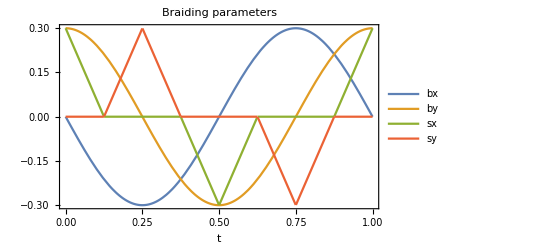

```mathematica
bn=-.3;
sn=+.3;
Bx[t_]:= +bn*Sin[t*2π]
By[t_]:= -bn*Cos[t*2π]
Sx[t_]:=sn*Piecewise[{ {1-1/.125t,0≤t≤.125},{-1/.125(t-.375),.375<t≤.5},{-1+1/.125(t-.5),.5<t≤.625},{+1/.125(t-.875),.875<t≤1}}]
Sy[t_]:=sn*Piecewise[{ {1/.125(t-.125),.125<t≤.25}, {1-1/.125(t-.25),.25<t≤.375}, {-1/.125(t-.625),.625<t≤.75}, {-1+1/.125(t-.75),.75<t≤.875}}]
Plot[{Bx[t],By[t],Sx[t],Sy[t]},{t,0,1},Frame->True,FrameLabel->{"t"},PlotLegends->{"bx","by","sx","sy"},PlotLabel->"Braiding parameters"]
```

```mathematica
Lx=Ly=100;(* momentum space discretization *)
NE=If[OddQ[Lx/4],Lx/4+1,Lx/4]; (* discretization of the DOS *)
kxs = Table[N[(2π)/Lx n]-π,{n,0,Lx-1}];
kys = Table[N[(2π)/Ly n]-π,{n,0,Ly-1}];
ts = Range[0,1,0.1];
ts={0,0.1};
```

```mathematica
pys ={};
pxs={};
wlps={};
WHs={};
pfaffianskx={};
pfaffiansky={};
basisplots={};
Monitor[
Do[
AbsoluteTiming[res =Table[{kx,ky,orderedGaugedEigensystem[H[kx,ky]/.{bz->0.,bx->Bx[t],by->By[t],sx->Sx[t],sy->Sy[t],s0->0.05}]},{kx,kxs},{ky,kys}];][[1]];(* parameters of their Fig. 8 in the SM *)
(*bands=Table[Flatten[Table[Join[res[[i,j,;;2]],{res[[i,j,3,1,b]]}], {i,Length[kxs]},{j,Length[kys]}],1],{b,Length[res[[1,1,3,1]]]}];*)
(*ListPlot3D[bands,MaxPlotPoints->Automatic,InterpolationOrder->1,Mesh->None, AxesLabel->{"k_x","k_y","E/λ"},PlotTheme->"Scientific"];*)
(*dos=DOS[Flatten[bands[[;;,;;,3]]],NE];*)
(*ListPlot[dos,FrameLabel->{"E/λ","ρ(E)"},Joined->True,PlotTheme->"Scientific"];*)
{WH1,WL1,NWL1,V1,UDU1} = nestedWilsonLoopxky[2,res];
AppendTo[WHs,WH1];
{WH2,WL2,NWL2,V2,UDU2} = nestedWilsonLoopykx[2,res];
pfkpi=Pfaffian[MatrixLog[WH1[[1]]]//Chop];
pfk0=Pfaffian[MatrixLog[WH1[[21]]]//Chop];
AppendTo[pfaffiansky,{{pfk0,pfkpi}}];
pfkpi=Pfaffian[MatrixLog[WH2[[1]]]//Chop];
pfk0=Pfaffian[MatrixLog[WH2[[21]]]//Chop];
AppendTo[pfaffianskx,{{pfk0,pfkpi}}];
wlp=GraphicsRow[{ListPlot[WL1ᵀ,PlotRange->0.5{-1,1},Joined->True,PlotTheme->"Scientific",DataRange->MinMax[kys]/π,FrameLabel->{"k_y/π","W_(x, SubscriptBox[k, y])"},AspectRatio->1], ListPlot[WL2ᵀ,PlotRange->0.5{-1,1},Joined->True,PlotTheme->"Scientific",DataRange->MinMax[kxs]/π,AspectRatio->1,FrameLabel->{"k_x/π","W_(y, SubscriptBox[k, x])"}]}];
AppendTo[wlps,wlp];
bp=GraphicsRow[Table[ListPlot[Mod[Arg[V1[[;;,n]]]ᵀ,2π]/π,PlotRange->{{0,2},{0,2}},Joined->True,DataRange->{0,2},PlotTheme->"Scientific",FrameLabel->{"k_x",StringForm["(W_(x, k))^(`1`)",n]}],{n,4}],ImageSize->2000];
AppendTo[basisplots,bp];
py=Mean[Mod[Im[Log[NWL1]],2π]]/(2π); (* polarization == 0.0, if |γ| > |λ| (triv. phase) *)
px=Mean[Mod[Im[Log[NWL2]],2π]]/(2π);(* polarization == 0.0, if |γ| > |λ| (triv. phase) *)
AppendTo[pys,py];
AppendTo[pxs,px];
,{t, ts}],t]
```

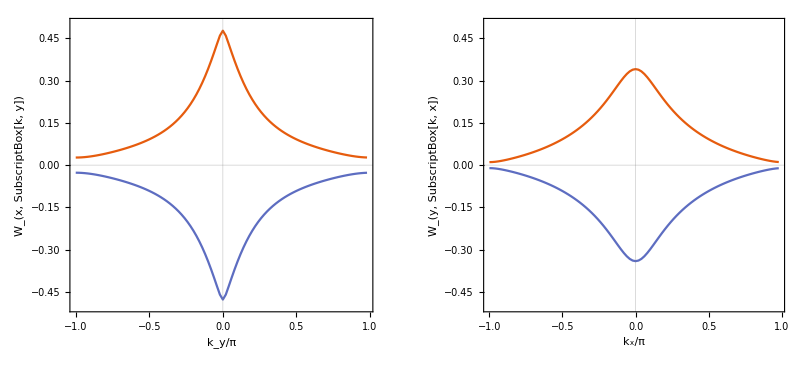
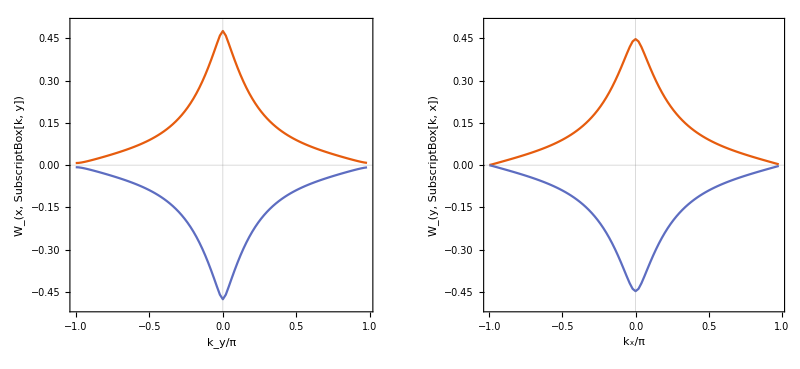

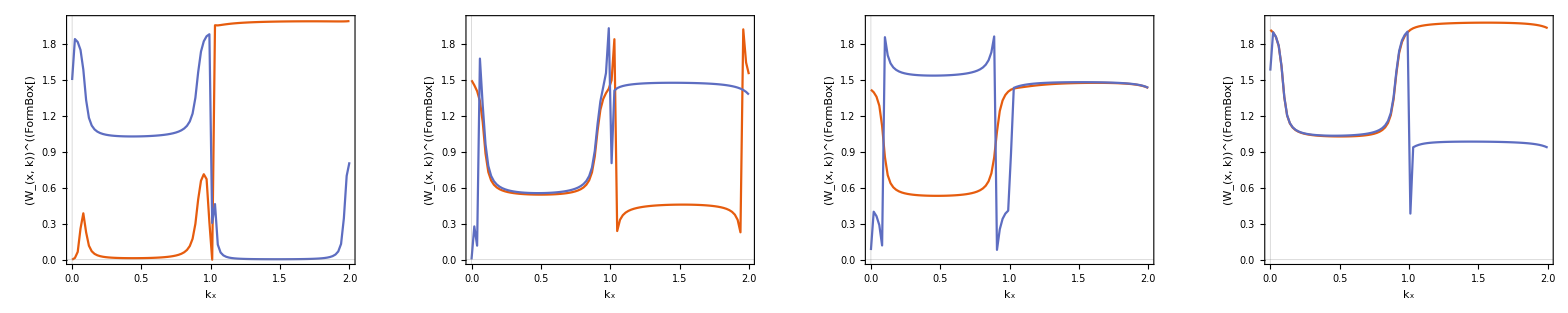

```mathematica
wlps
basisplots[[1]]
```

```mathematica
tsel=2;
k=11;
LogUnitary[Unitarize[WHs[[tsel,1]]]][[1]]//Chop//MatrixForm;
LogUnitary[Unitarize[WHs[[tsel,21]]]][[1]]//Chop//MatrixForm;
WHk=Unitarize[WHs[[tsel,k]]];
WHmk=Unitarize[WHs[[tsel,-(k-1)]]];
{logWHk, ek, vk}=LogUnitary[WHk];
{logWHmk, emk, vk}=LogUnitary[WHmk];
MatrixExp[ⅈ * logWHk]-WHk//Chop//MatrixForm
MatrixExp[ⅈ * logWHmk] - WHmk//Chop//MatrixForm
{Table[StringForm["σ``",i],{i,0,3}],Table[Norm[logWHk-σ.logWHmk*.σ//Chop],{σ,Table[PauliMatrix[i],{i,0,3}]}]}//TableForm
logWHk//MatrixForm//Chop
logWHmk*//MatrixForm//Chop
```

(0 | 0
0 | 0)

(0 | 0
0 | 0)

σ0 | σ1 | σ2 | σ3
0.37879 | 0.382844 | 0.0995087 | 0.0357799

(0.0383457 | 0.18372+0.0493014 ⅈ
0.18372-0.0493014 ⅈ | -0.0383457)

(0.0381705 | -0.189738-0.0140314 ⅈ
-0.189738+0.0140314 ⅈ | -0.0381705)

```mathematica
k=12;
LogUnitary[Unitarize[WHs[[tsel,1]]]][[1]]//Chop//MatrixForm;
LogUnitary[Unitarize[WHs[[tsel,21]]]][[1]]//Chop//MatrixForm;
WHk=Unitarize[WHs[[tsel,k]]];
WHmk=Unitarize[WHs[[tsel,-(k-1)]]];
{logWHk, ek, vk}=LogUnitary[WHk];
{logWHmk, emk, vk}=LogUnitary[WHmk];
MatrixExp[ⅈ * logWHk]-WHk//Chop//MatrixForm
MatrixExp[ⅈ * logWHmk] - WHmk//Chop//MatrixForm
{Table[StringForm["σ``",i],{i,0,3}],Table[Norm[logWHk-σ.logWHmk*.σ//Chop],{σ,Table[PauliMatrix[i],{i,0,3}]}]}//TableForm
logWHk//MatrixForm//Chop
logWHmk*//MatrixForm//Chop
```

(0 | 0
0 | 0)

(0 | 0
0 | 0)

σ0 | σ1 | σ2 | σ3
0.417556 | 0.421614 | 0.100516 | 0.0401695

(0.0386586 | 0.203194+0.0519265 ⅈ
0.203194-0.0519265 ⅈ | -0.0386586)

(0.0384624 | -0.209402-0.0122401 ⅈ
-0.209402+0.0122401 ⅈ | -0.0384624)